# CoffeeCode Interface

Set the CoffeeCode release path below (where you execute make), and the file you configured as cc-instance-custom.h during ccmake. You can use the file open dialogue helper to obtain said paths.

```mathematica
SystemDialogInput["Directory"]
SystemDialogInput["FileOpen"]
```

```mathematica
CCRELEASEPATH="/home/jkrb2/programming/CoffeeCode/build/release/";
CCCUSTOMINSTANCEFILE="/home/jkrb2/programming/CoffeeCode/build/release/cc-instance-custom.h";
```

## Basic Graph Functionality [install IGraphM once below, then forget]

### IGraphM

Uncomment the last line in the following cell, then execute to install IGraphM. This only has to be done once per machine.

```mathematica
updateIGraphM[]:=Module[{json,download,target,msg},Check[json=Import["https://api.github.com/repos/szhorvat/IGraphM/releases","JSON"];
download=Lookup[First@Lookup[First[json],"assets"],"browser_download_url"];
msg="Downloading IGraph/M "<>Lookup[First[json],"tag_name"]<>" ...";
target=FileNameJoin[{CreateDirectory[],"IGraphM.paclet"}];
If[$Notebooks,PrintTemporary@Labeled[ProgressIndicator[Appearance->"Necklace"],msg,Right],Print[msg]];
URLSave[download,target],Return[$Failed]];
If[FileExistsQ[target],PacletManager`PacletInstall[target],$Failed]]
(*updateIGraphM[]*) (* uncomment this once and run to install IGraphM locally, then comment again *)
```

```mathematica
<<IGraphM`
ParallelEvaluate[<<IGraphM`;];
```

IGraph/M 0.3.103 (November 13, 2018)

Evaluate IGDocumentation[] to get started.

IGraph/M 0.3.103 (November 13, 2018)

IGraph/M 0.3.103 (November 13, 2018)

Evaluate IGDocumentation[] to get started.

Evaluate IGDocumentation[] to get started.

IGraph/M 0.3.103 (November 13, 2018)

Evaluate IGDocumentation[] to get started.

IGraph/M 0.3.103 (November 13, 2018)

Evaluate IGDocumentation[] to get started.

```mathematica
Clear[EnvironmentVertexLinkColoring,GroupForGraph]
EnvironmentVertexLinkColoring[graph_Graph,kSys_Integer]:=EnvironmentVertexLinkColoring[graph,kSys]=Module[{
environmentVertices=VertexList[graph]⟦kSys+1;;⟧,
coloredVertexIndices,
vertexColors
},
coloredVertexIndices=VertexIndex[graph,#]&/@AdjacencyList[graph,environmentVertices];
Normal@SparseArray[Thread[coloredVertexIndices->1],{kSys}]
]

GroupForGraph[graph_Graph,kSys_Integer]:=GroupForGraph[graph,kSys]=Module[{
gSys=Subgraph[graph,VertexList[graph]⟦;;kSys⟧],
vertexColors=EnvironmentVertexLinkColoring[graph,kSys]
},

PermutationGroup[
PermutationCycles/@IGBlissAutomorphismGroup[{gSys,"VertexColors"->vertexColors}]
]
]
```

### Plot Graph

```mathematica
Clear[EnvironmentPlot]
EnvironmentPlot[g_Graph,systemSize_]:=Graph[g,VertexStyle->(
Thread[(Range[VertexCount@g-systemSize]+systemSize)->Red]
),VertexSize->.2,VertexLabels->None]
```

### Create all Possible Choices of Hairs to the Environment

```mathematica
Clear[IsomorphicHairChoiceQ,HairColoring]
HairColoring[hairs_]:=HairColoring[Sort@hairs]=Length/@GroupBy[hairs,Identity]
IsomorphicHairChoiceQ[g_Graph,hairs1_,hairs2_]:=IsomorphicHairChoiceQ[g,hairs1,hairs2]=IsomorphicHairChoiceQ[g,hairs2,hairs1]=IGVF2IsomorphicQ[
{g,"VertexColors"->HairColoring@hairs1},
{g,"VertexColors"->HairColoring@hairs2}
]
IsomorphicHairChoiceQ[g_Graph]:=IsomorphicHairChoiceQ[g,#1,#2]&
```

```mathematica
Clear[HairGraph,AllHairGraphs]
HairGraph[g_,hairs_]:=HairGraph[g,hairs]=With[{
new=VertexCount@g+Range@Length@hairs
},
EdgeList[g]~Join~Thread[hairs<->new]//Graph
]
AllHairGraphs[g_,generator_:Hold[Subsets[#]⟦2;;⟧&]]:=AllHairGraphs[g,generator]=With[{
(* first check for graph isomorphism using a vertex coloring *)
uniqueHairEndpoints=DeleteDuplicates[
ReleaseHold[generator][VertexList@g],
IsomorphicHairChoiceQ[g]
]
},
HairGraph[g,#]&/@uniqueHairEndpoints
]
```

### Strong Generating Set Transversal

```mathematica
Clear[SGSTransversal]
(* the head element of the group stabilizer chain already delivers a transversal of a strong generating set *)
SGSTransversal[group_PermutationGroup]:=With[{
chain=GroupStabilizerChain[group]
},
Partition[chain,2,1]/.{Rule[sA_,gA_],Rule[sB_,gB_]}:>(
Complement[sB,sA]->PermutationGroup@Complement[GroupGenerators@gA,GroupGenerators@gB]
)
]
```

## Export Functions

### Exporting MM symbols

```mathematica
Clear[ExportAdjacencyMatrix]
ExportAdjacencyMatrix[g_Graph]:=With[{
Avec=g//AdjacencyMatrix//Normal//Flatten
},
StringJoin[ToString/@Avec]
]
```

```mathematica
Clear[SGSTransversalMMForm]
SGSTransversalMMForm[list_List,length_Integer]:=list/.{
Rule[{idx_Integer},PermutationGroup[cycles_List]]:>Module[{
permutationIndices=PermutationList[#,length]&/@cycles
},

(* the pivot point is the first index for which the SGSGenerator acts nontrivially on (so one point past the points that are stabilized).
If the pivot point for the SGSGenerator is 2, that means we want to check indices 0 and 1 in C++; in MM this would correspond to indices {1, 2}, which is what ⟦;;2⟧ truncates to.
Therefore we validly don't subtract 1 from the pivot point, but do subtract 1 from all other indices *)
StringRiffle[Flatten@{
"\tSGSGenerator<"<>ToString@(#1)<>", Group<",
("\t\tPermutation<"<>StringRiffle[ToString/@(##-1),","]<>">")&/@#2,
"\t>>"
},"\n"]&@@{idx,permutationIndices}

]
}//Flatten//("using sgs = SGSTransversal<\n"<>StringRiffle[#,",\n"]<>"\n>;")&
```

```mathematica
Clear[ExportSymmetricCCInstance]
ExportSymmetricCCInstance[graph_Graph,kSys_Integer,name_:"graphstate_instance"]:=With[{
sgs=SGSTransversal@GroupForGraph[graph,kSys],
adj=ExportAdjacencyMatrix@graph,
kTot=VertexCount@graph
},

If[Length@sgs==0,Echo["WARN: symmetry group is 0. Not a valid symmetric problem instance."]];

"struct "<>name<>" {\n"<>
SGSTransversalMMForm[sgs,kSys]<>"\n"<>
"constexpr static size_t k_sys = "<>ToString[kSys]<>", k_env = "<>ToString[kTot-kSys]<>";\n"<>
"constexpr static AdjacencyMatrixT<"<>ToString[kTot]<>"> adjacency_matrix{"<>ToString[Normal@AdjacencyMatrix@graph]<>"};\n"<>
"};"
]
```

### Build Interface

```mathematica
Clear[MakeCC]
MakeCC[kSys_Integer,kEnv_Integer]:=With[{
out=RunProcess[
{
"make",
"-B",
"K_SYS="<>ToString@kSys,
"K_ENV="<>ToString@kEnv
},
ProcessDirectory->CCRELEASEPATH
]
},
out["ExitCode"]==0
]
MakeCC[graph_Graph,kSys_Integer]:=With[{
instanceFileContent=ExportSymmetricCCInstance[graph,kSys]
},
Export[CCCUSTOMINSTANCEFILE,instanceFileContent,"Text"];
MakeCC[kSys,VertexCount@graph-kSys]
]
```

```mathematica
MakeCC[3,1]
```

True

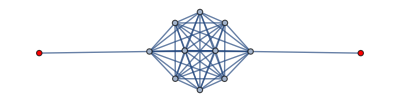
```mathematica
MakeCC[-Graphics-,10]
```

True

```mathematica
Clear[RunCC]
RunCC[graph_Graph,kSys_Integer]:=With[{},
If[!MakeCC[graph,kSys],
Return[False]
];

With[{
ccResult=RunProcess["CoffeeCode",ProcessDirectory->CCRELEASEPATH]
},
If[ccResult["ExitCode"]≠0,
Return[False]
];

ImportString[ccResult["StandardOutput"],"RawJSON"]
]
]
```

```mathematica
RunCC[-Graphics-,10]
```

## Interface

#### Create graphs by hand

To create graphs by hand, look up the following functions:

```mathematica
AdjacencyGraph
SparseArray
PathGraph
```

Or directly use MM’s Graph object, where edges are entered with ESC ue ESC

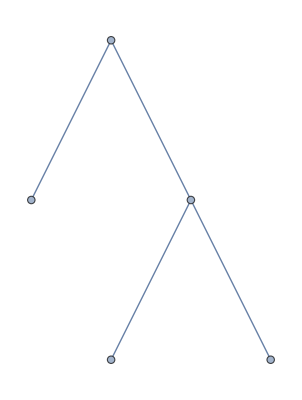

```mathematica
Graph[{1<->2,3<->4,3<->5,1<->3}]
```

#### Create a random graph, add a hair, and plot.

```mathematica
CompleteGraph[10];
HairGraph[%,{10,9}];
graph=EnvironmentPlot[%,10]
```

-Graphics-

#### Export instance

Just adjacency matrix for Full Solver

```mathematica
ExportAdjacencyMatrix[graph]
```

011111111100101111111100110111111100111011111100111101111100111110111100111111011100111111101100111111110101111111111010000000000100000000001000

SGS for Symmetric Solver

```mathematica
ExportSymmetricCCInstance[graph,10]
Export[SystemDialogInput["FileSave"],%,"Text"]
```

struct graphstate_instance {
using sgs = SGSTransversal<
	SGSGenerator<1, Group<
		Permutation<1,0,2,3,4,5,6,7,8,9>
	>>,
	SGSGenerator<2, Group<
		Permutation<0,2,1,3,4,5,6,7,8,9>
	>>,
	SGSGenerator<3, Group<
		Permutation<0,1,3,2,4,5,6,7,8,9>
	>>,
	SGSGenerator<4, Group<
		Permutation<0,1,2,4,3,5,6,7,8,9>
	>>,
	SGSGenerator<5, Group<
		Permutation<0,1,2,3,5,4,6,7,8,9>
	>>,
	SGSGenerator<6, Group<
		Permutation<0,1,2,3,4,6,5,7,8,9>
	>>,
	SGSGenerator<7, Group<
		Permutation<0,1,2,3,4,5,7,6,8,9>
	>>,
	SGSGenerator<9, Group<
		Permutation<0,1,2,3,4,5,6,7,9,8>
	>>
>;
constexpr static size_t k_sys = 10, k_env = 2;
constexpr static AdjacencyMatrixT<12> adjacency_matrix{{{0, 1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 0}, {1, 0, 1, 1, 1, 1, 1, 1, 1, 1, 0, 0}, {1, 1, 0, 1, 1, 1, 1, 1, 1, 1, 0, 0}, {1, 1, 1, 0, 1, 1, 1, 1, 1, 1, 0, 0}, {1, 1, 1, 1, 0, 1, 1, 1, 1, 1, 0, 0}, {1, 1, 1, 1, 1, 0, 1, 1, 1, 1, 0, 0}, {1, 1, 1, 1, 1, 1, 0, 1, 1, 1, 0, 0}, {1, 1, 1, 1, 1, 1, 1, 0, 1, 1, 0, 0}, {1, 1, 1, 1, 1, 1, 1, 1, 0, 1, 0, 1}, {1, 1, 1, 1, 1, 1, 1, 1, 1, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0}}};
};

Export::chtype: First argument $Canceled is not a valid file specification.

$Failed